```mathematica
Limit[D[(4x(E^x+1)-8(E^x-1)), x]/D[(6x^3),x], x-> 0]

stev = FullSimplify[D[4x(e^x+1)-8(e^x-1), x]];

ime = D[6x^3, x];
imen = Simplify[%]

Limit[stev/imen, x->0]
```

1/9

18 x^2

DirectedInfinity[2-2 Log[e]]

Root::rnum: x is not a valid root number.

Root[1/27 ⅇ^(3 x) (-430-6 x+63 x^2+9 x^3),x]

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-6},{x→-4},{x→2}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

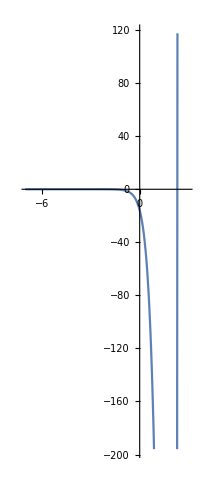

```mathematica
f1 = 1/27E^(3x)*(9x^3+63x^2-6x-430);

Root[f1, x]
Solve[D[f1,x]==0,x] 
FullSimplify[Solve[D[f1,x]==0,x]];
Plot[f1, {x,-7,3}, AspectRatio->Full]
```

```mathematica
prem1 = -8x+5y-1=0;
prem2 = -5x+y+7=0;
Solve[prem1,prem2, {x,y}]
Solve[{-8x+5y-1=0, -5x+y+7=0}, {x,y}]
36/17 // N
61/17 // N
```

Set::write: Tag Plus in -1+48+5 y is Protected.

Set::write: Tag Plus in 7+30+y is Protected.

Solve::ivar: 0 is not a valid variable.

Solve[0,0,{-6,y}]

Set::write: Tag Plus in -1+48+5 y is Protected.

Set::write: Tag Plus in 7+30+y is Protected.

Solve::ivar: -6 is not a valid variable.

Solve[{0,0},{-6,y}]

2.11765

3.58824

General::ivar: -6 is not a valid variable.

General::ivar: 3 is not a valid variable.

∂_3 (-6 ⅈ √5)

General::ivar: -6 is not a valid variable.

General::ivar: 3 is not a valid variable.

∂_3 (-6 ⅈ √5)

6-9 ∂_3 (-6 ⅈ √5)

-1/(∂_3 (-6 ⅈ √5))

6+9/(∂_3 (-6 ⅈ √5))

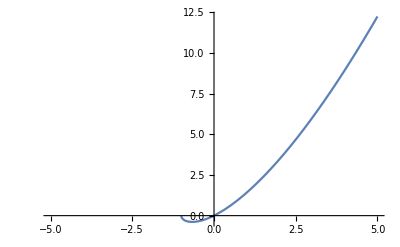

```mathematica
f=x*Sqrt[1+x];
y0 =3*Sqrt[1+3];
x0=3; y0;  (* točka za tangento in normale *)
kt=D[x*Sqrt[1+x],x]/.x->3
kt=D[f,x]/.x->x0   (* smerni koef tangente *)
nt=y0-kt*x0;  (* začetna vrednost tangente *)
y=kt*x+nt   (* enačba tangente *)
kn=-1/kt   (* smerni koef normale *)
nn=y0-kn*x0;   (* začetna vrednost normale *)
y=kn*x+nn  (* enačba normale *)
Plot[x*Sqrt[1+x], {x, -5, 5}]
```

{{x→-4}}

46

94

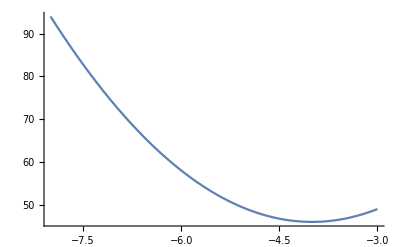

```mathematica
Clear["Global`*"]
f=3x^2+24x+94;
Solve[D[f,x]==0,x]
f/.x->-4
f/.x->-8
Plot[3x^2+24x+94, {x, -8, -3}]
```

```mathematica
Clear["Global`*"]

Limit[(-4x^2-28x+32)/(x-1), x->1]
Limit[D[(-4x^2-28x+32),x]/D[(x-1),x], x->1]
```

-36

-36

-2<x<-1

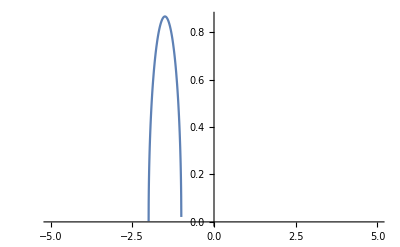

```mathematica
Clear["Global`*"]

Reduce[Sqrt[-3x^2-9x-6]>0]
Plot[Sqrt[-3x^2-9x-6], {x, -5, 5}]
```

{{x→-4},{x→-1}}

41

5

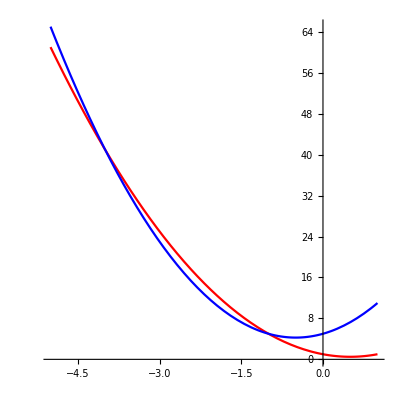

```mathematica
(* Parabola *)
Clear["Global`*"]
kr1=2x^2-2x+1;
kr2 = 3x^2+3x+5;
Solve[{kr1 == kr2}, x]

kr1 /. x->-4
kr1 /. x->-1
Plot[{kr1, kr2}, {x, -5, 1}, PlotStyle->{Red, Blue}, AspectRatio->1]
```

{{x→0},{x→5}}

True

True

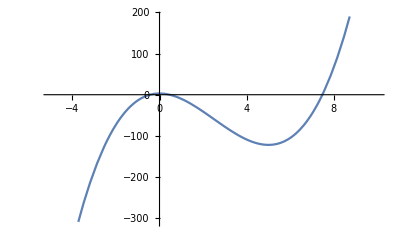

```mathematica
Clear["Global`*"]
f=2x^3-15x^2+3;
Solve[D[f, x]==0,x]
(D[f,x,x]/.x->0)<0
(D[f,x,x]/.x->5)>0
Plot[f, {x, -5, 10}]
```

```mathematica
Clear["Global`*"]
f=-3x^4+2x^3-5x^2+5;
D[f,x]
(D[f,x] /. x->1)
```

-10 x+6 x^2-12 x^3

-16